```mathematica
ClearAll["Global`*"]
```

# Lifetime Model

## Constants

```mathematica
ℏ = 1.0545718*10^-34;
m = 171*1.6726219*10^-27;
μB = 9.274009994*10^-24;
e=1.60217662*10^-19;
kB = 1.38064852*10^-23;
```

## Parameters

### Trapped Ion System Parameters

```mathematica
dzB = 23.6;
η = 0.046; (* geometric factor *)
d = 310 10^-6;  (* distance to electrodes *)
```

### Voltage Noise Parameters

```mathematica
StahlEnFlicker = (3.0 10^-6)^2 (* Stahl flicker noise, V^2/Hz*);
StahlEnWhite = (12.6 10^-9)^2 (* Stahl white noise, V^2/Hz*);
Forder = 4; (* Order of low pass filter *)
ωc = 2 π 30.5; (* Cutoff frequency of low pass filter *)
```

### Magnetic Field Noise Parameters

```mathematica
Bnoisefloor = (1 10^-12)^2; (* Magnetic field noise floor T^2/Hz *)
```

## Functions

### Voltage Noise Functions

```mathematica
Flp[ω_,ωc_, n_]:=1/(√(1+(ω/ωc)^(2*n)))  ;  (* Butterworth filter function *)
SJsim[ω_] := ((G0(1 + ((2 π ω)/ωcj)^(2n))^-1.5)^2/.{G0-> 8.19 10^-9, ωcj-> 2 π 6.5 10^3, n-> .34} )+ (4 kB 300 0.4);  (* Thermal noise simulated with LT spice *)
SJexp[ω_] := 200((G0(1 + ((2 π ω)/ωcj)^(2n))^-1.5)^2/.{G0-> 8.19 10^-9, ωcj-> 2 π 6.5 10^3, n-> .34} )+ (4 kB 300 0.4); (* Thermal noise adjusted to fit experimental data. There is a pre factor of 200 because the simulated thermal noise was lower than what we found experimentally. The pre factor was determined by rebuilding the spectrum with lifetime measurements.*)

Ss[ω_] := If[ω < 0.1,StahlEnFlicker/(0.1/(2π)) , StahlEnFlicker/(ω/(2π))] + StahlEnWhite; (*Noise out of Stahl, 1/f noise (ie StahlEnFlicker) was measured, Broadband noise taken from spec sheet. Stahl specs are 0.1 Hz - 1 Hz -> 0.015 mVrms, and 10 Hz - 10 MHz -> 0.04 Vrms *)

Sf[ω_] := Ss[ω] Flp[ω,ωc, Forder]^2 ; (* PSD out of filter *)

Sg[ω_] := (A Exp[-(ω - ω0)^2/(2 σ^2)])^2 /.{A-> 7 10^-9, ω0-> 2π 20 10^3, σ-> 2 π 4 10^3} (* We discovered some noise at 20 kHZ. Model it as some Gaussian, and we fit it to experimental data. *)

SV[ω_] := Abs[Sf[ω]  +  SJexp[ω] + Sg[ω] ]; (* Final voltage PSD on electrodes *)
```

### Magnetic Field Noise Functions

```mathematica
dBdV[ω_, ν_] := (e dzB η)/(m d (ν^2 - ω^2)); (* Convert Voltage Noise to Magnetic Field Noise *)
dBdE[ω_, ν_] := (e dzB)/(m  (ν^2 - ω^2)); 
SB[ω_, ν_] := dBdV[ν, ω]^2 SV[ω]  + Bnoisefloor(* Magnetic field Power Spectral Density *)
```

### Lifetime Functions

```mathematica
T1[ω_, ν_] := 1/(2π)(ℏ/μB)^2 SB[ω, ν]^-1;
```

```mathematica
Sb =  1/(2π)(ℏ/μB)^2/t1/.{t1-> 0.1};
Se = Sb dBdE[1, 2π 221 10^3]^-2;
√Se
```

2.09235×10^-6

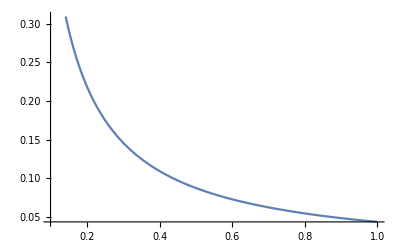

```mathematica
T1E[se_] := 1/(2π)(ℏ/μB)^2(se dBdE[1, 2π 221 10^3]^2)^-1
Plot[T1E[se], {se, 10^-12, 10^-11}]
```

## Power Spectral Density

### Voltage PSD

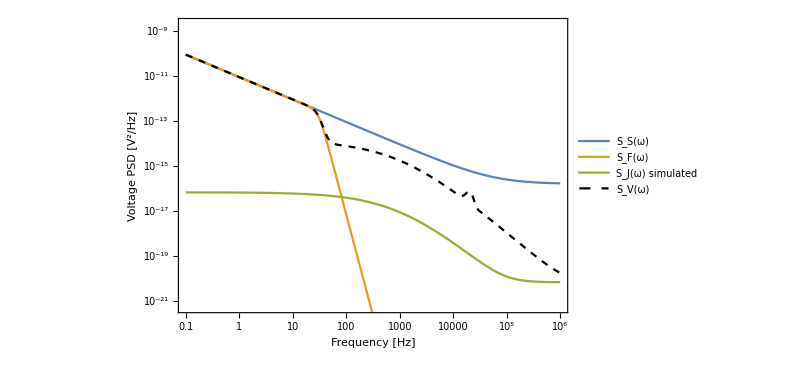

```mathematica
Show[LogLogPlot[{Ss[2 π ω], Sf[2 π ω], SJsim[2 π ω], SV[2 π ω]}, {ω, 0.1, 1000 10^3}, PlotStyle-> {Automatic, Automatic, Automatic, {Black, Thick, Dashed}}, PlotLegends-> {"S_S(ω)", "S_F(ω)", "S_J(ω) simulated", "S_V(ω)"}],
Frame-> True, ImageSize-> 600, PlotRange-> {All,{-49, -20}}, Axes-> False, FrameStyle-> Directive[{Thick, 15}], LabelStyle-> Directive[ 25, Black], FrameLabel-> {"Frequency [Hz]", "Voltage PSD [V^2/Hz]"}]
```

### Magnetic Field PSD

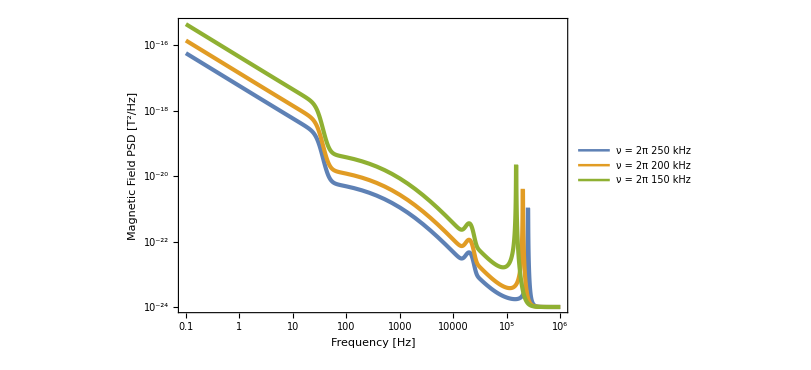

```mathematica
Show[LogLogPlot[{SB[2 π ω, 2 π 250 10^3], SB[2 π ω, 2 π 200 10^3], SB[2 π ω, 2 π 150 10^3]}, {ω, 0.1, 1000 10^3}, PlotStyle-> Directive[Thickness[0.005]], PlotLegends-> {"ν = 2π 250 kHz", "ν = 2π 200 kHz", "ν = 2π 150 kHz"}],
Frame-> True, ImageSize-> 600, PlotRange-> All, Axes-> False, FrameStyle-> Directive[{Thick, 15}], LabelStyle-> Directive[ 25, Black], FrameLabel-> {"Frequency [Hz]", "Magnetic Field PSD [T^2/Hz]"}]
```

## Expected Lifetime

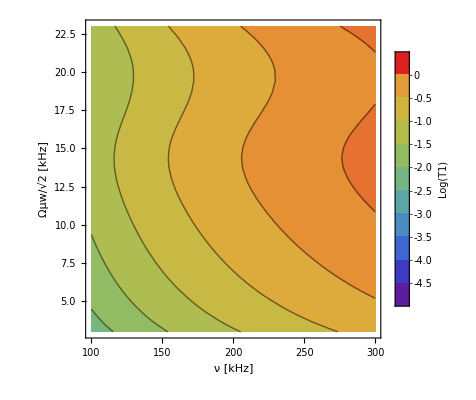

```mathematica
barlegend = BarLegend[{"Rainbow",{-5,1}},  {-5,-4.5,-4,-3.5,-3, -2.5,-2,-1.5, -1,-0.5, 0}, LegendLabel->"Log(T1)"];
Legended[Show[ContourPlot[Log10[T1[ 2 π Ω 10^3, 2π ν 10^3]], {ν, 100, 300}, {Ω, 3, 23},
ColorFunction->ColorData[{"Rainbow", {-6, 1}}], ColorFunctionScaling->False],
 ImageSize-> 400, LabelStyle-> {Black, Bold, 12}, FrameLabel-> {"ν [kHz]", "Ωμw/√2 [kHz]"}, FrameStyle-> Directive[15]], barlegend]
```